```mathematica
Semismooth Newton Method's




SemismoothNewtonMethod[f_,Df_,x0_,dimension_,error_,interacje_]:=
Module[{xk,k,d,Vk,lista},
k=0;
Vk=Df[x0];
xk=x0;
lista={};
While[Norm[f[xk]]>error &&k<interacje,
AppendTo[lista,Norm[f[xk]]];

Vk=Df[xk];

(*Print["Vk ",Vk];*)
(*Print["k ",k," f[xk] ",f[xk]," xk ",xk];*)
d=-(Inverse[Vk]*f[xk]);

xk=xk+d;
k++;
(*Print[xk," xk"];*)
];
(*Print["k ",k," f[xk] ",f[xk]," xk ",xk];*)
Flatten[lista]
]

DampedModifiedSemismoothNewtonMethod[f_,Df_,x0_,v0_,rho_,sigma_,dimension_,error_,interacje_]:=
Module[{xk,k,d,Vk,Merit,DivMerit,lambda,lista},
k=0;
Vk=Df[x0];
xk=x0;
Merit[x_]:={{(1/2)*Norm[f[x]]^2}};
DivMerit[x_]:=Transpose[Df[x]]*f[x];

lista={};
While[Norm[f[xk]]>error &&k<interacje,
AppendTo[lista,Norm[f[xk]]];
Vk=Df[xk];



d=-(Inverse[Vk].f[xk]);


For[i=0,
Part[Merit[xk+rho^i*d]-Merit[xk],1,1]>Part[sigma*rho^i*Transpose[DivMerit[xk]].d,1,1],
i++;
];

lambda=rho^i;
xk=xk+lambda*d;
k++;
(*Print[xk," xk"];*)
];


Flatten[lista]
]


DampedModifiedSemismoothGaussNewtonMethod[f_,Df_,x0_,v0_,rho_,sigma_,dimension_,error_,interacje_]:=
Module[{xk,k,d,Vk,Merit,DivMerit,lambda,lista},
k=0;
Vk=Df[x0];
xk=x0;
Merit[x_]:={{(1/2)*Norm[f[x]]^2}};
DivMerit[x_]:=Transpose[Df[x]]*f[x];
Print["start"];
lista={};
While[Norm[f[xk]]>error&&k<interacje,
AppendTo[lista,Norm[f[xk]]];
Vk=Df[xk];



d=-(Transpose[Vk].f[xk]).Inverse[Transpose[Vk].Vk+v0*IdentityMatrix[dimension]];



For[i=0,
Part[Merit[xk+rho^i*d]-Merit[xk],1,1]>Part[sigma*rho^i*Transpose[DivMerit[xk]].d,1,1],
i++;
];



lambda=rho^i;
xk=xk+lambda*d;
k++;
(*Print[xk," xk"];*)
];

(*Print["k ",k," f[xk] ",f[xk]," xk ",xk];*)
Flatten[lista]
]
```

```mathematica
f[x_]:={{Part[x,1,1]^3-5*Part[x,1,1]}}
```

```mathematica
Df[x_]:={{3*Part[x,1,1]^2-5}}
```

start

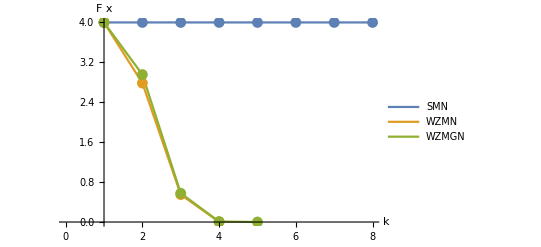

```mathematica
ListLinePlot[{SemismoothNewtonMethod[f,Df,{{1}},1,0.0001,8],DampedModifiedSemismoothNewtonMethod[f,Df,{{1}},0.5,0.2,0.3,1,0.0001,8],DampedModifiedSemismoothGaussNewtonMethod[f,Df,{{1}},0.5,0.2,0.3,1,0.0001,8]},PlotLegends-> {SMN,WZMN,WZMGN},AxesLabel->{k,F(x)},AxesOrigin->{1,0},Mesh->All]
```

```mathematica
f1[x_]:={{Max[Part[x,1,1],Part[x,1,1]^2]}}
```

```mathematica
Df1[arg1_]:=
Module[{el,result},
el=Part[arg1,1,1];
result=Which[(el< 0 || el>1) , 
				{{2*el}},
				(el>0 && el<1 ),
				{{1}},
				(el==0  || el==1),
				{{(2*el+1)/2}}
			]
		]
```

start

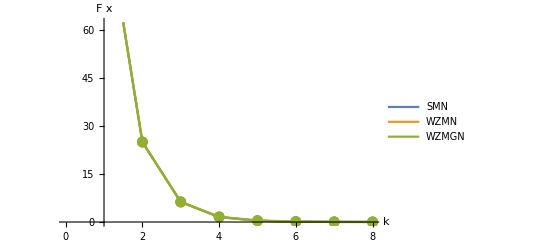

```mathematica
ListLinePlot[{SemismoothNewtonMethod[f1,Df1,{{-10}},1,0.0001,8],DampedModifiedSemismoothNewtonMethod[f1,Df1,{{-10}},0.5,0.2,0.3,1,0.0001,8],DampedModifiedSemismoothGaussNewtonMethod[f1,Df1,{{-10}},0.5,0.2,0.3,1,0.0001,8]},PlotLegends-> {SMN,WZMN,WZMGN},AxesLabel->{k,F(x)},AxesOrigin->{1,0},Mesh->All]
```

```mathematica
f3[x_]:={{Log[1+Norm[Part[x,1,1]]]}}
```

```mathematica
Df3[arg1_]:=
Module[{el,result},
el=Part[arg1,1,1];
result=Which[( el>0) , 
				{{1/(1+el)}},
				(el< 0 ),
				{{-1/(1-el)}},
				(el==0  ),
				{{0}}
			]
		]
```

start

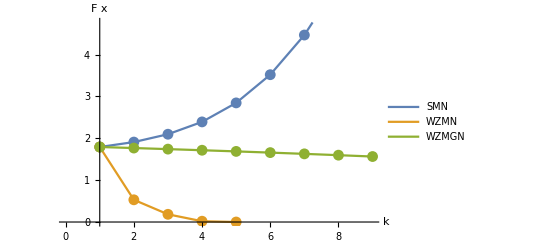

```mathematica
ListLinePlot[{SemismoothNewtonMethod[f3,Df3,{{5}},1,0.0001,9],DampedModifiedSemismoothNewtonMethod[f3,Df3,{{5}},2,0.4,0.4,1,0.0001,9],DampedModifiedSemismoothGaussNewtonMethod[f3,Df3,{{5}},2,0.4,0.4,1,0.0001,9]},PlotLegends-> {SMN,WZMN,WZMGN},AxesLabel->{k,F(x)},AxesOrigin->{1,0},Mesh->All]
```